# Empirical Analysis of P vs. NP: On the Equivalence of Turing Machines as Partial Functions

Michael Sun

Wolfram Summer Research Program 2025
Edited 18 September 2025

A Turing machine is a theoretical model of computation classified as an automaton invented by Alan Turing that operates on an infinite tape of sequential memory. The significance of Turing machines, as described in the Church-Turing thesis, comes from their ability to compute any function and therefore have the same computational ability as all conventional computers. Empirical evidence suggests that there exists Turing machines that follow different rules but ultimately compute the same function, presumably for all inputs. Naturally, these machines will have different runtimes, which models multiple computers running different algorithms to reach the same goal. Similarly, motivation for studying complexity theory comes from analyzing and improving algorithms. A central unsolved problem in the field is if quickly verifying a solution to a problem implies the existence of an algorithm that quickly solves it—commonly known as the P vs. NP problem. Analyzing patterns in the range of runtimes for equivalent Turing machines provides potential for empirically hypothesizing at the relationship between P and NP.

## Introduction

Formally, a Turing machine is a tuple containing a set of states, a halt state, a set of symbols called its alphabet, and a lookup table of all possible state-symbol pairs. Turing machines keep a pointer to the cell it is currently reading, and the symbol on this cell combined with its current state defines a transition. For each transition, three operations occur: read the symbol on the current cell, write a (not necessarily distinct) symbol to the current cell, and move to an adjacent cell. Certain traits of a Turing machine are difficult to quickly represent with a computer, so the results in this essay will be close approximations of the real behavior of Turing machines. Specifically, we will bound a finite section of the tape and set a halting condition not dependent on its state for convenience.

### Terminology

In this essay, the variables  and  generally refer to the  states and  symbols of a Turing machine, and the ordered pair  refers to an -state -symbol Turing machine. Additionally, we define setting a Turing machine to a nonnegative integer  as filling our chosen interval  of the tape of length  for some  with the binary representation of  in big endian (natural left-to-right order). We ensure that  (i.e. the number of bits fits in ). Additionally, we define the value of a Turing machine as the number created by each cell on  as base- digits where the blank symbol translates to zero (which is automatic in the Wolfram Language).

### Formalism

Let  be the set of all -state -symbol Turing machines. Each machine in  represents a partial function ⇀ on a fixed interval  of length  on the tape where  is the set of symbols and  is the set of input symbols. For this project, we set . Equivalently, this function can also be represented as ℕ⇀ℕ with input specified by the base  number formed on  where each symbol is an integer between 0 and . Define two Turing machines in  to be equivalent if they compute the same partial function on , or both do not exist. The number of distinct machines is the cardinality of . For each equivalence class, we will analyze patterns of the worst-case running times of each machine in the class and over all classes in  for different  and .

For example, the following 2-state 2-symbol Turing machine takes in  where 1’s are colored orange. The output is read as . It turns out that this rule always adds 1 to the input for our constraints.

Evolution of the partial function  described by rule 451 for  and input :

```mathematica
RulePlot[TuringMachine[445],{{1,4},{IntegerDigits[5,2,4],0}},5,ImageSize->Small]//Rasterize
```

-Graphics-

### Theory

Only certain  pairs are capable of simulating any other Turing machine starting from a blank tape. For example, any Turing machine with one symbol trivially fails to be universal because it will not edit the tape. Pairs that can simulate all other machines are known as universal Turing machines. Additionally, weakly universal Turing machines are machines that are universal on an arbitrary initial tape. Notably, the smallest of these machines are fully analyzable within computational constraints, such as , , and Wolfram’s  machine.

The universality of Turing machines as a mathematical model of computation revealed limits of computing, notably cases of logical (un)decidability. A problem is undecidable if and only if it is provable that there exists no algorithm that will always return the correct answer to the problem. Turing’s major result was his proof of the undecidability of determining if a computer program halts, famously known as the halting problem.

#### The Halting Problem and Rice’s Theorem

The usefulness of the undecidability of the halting problem is not only limited to the statement itself, but because many problems can be shown to be undecidable by reducing them to the halting problem. More notably, it is undecidable to determine if two Turing machines are equivalent, which necessitates the mentioned constraints. Similarly, the task to quickly analyze the behavior of a Turing machine without simulating it is a generalization of the halting problem known as Rice’s theorem, which implies that this task is generally undecidable. However, it does not say anything about determining relationships between machines, which we will see in a later section could contain a predictable pattern.

## Implementation

Due to the undecidability of universal static analysis and the computational irreducibility of Turing machine evolution, the implementation will inevitably be brute-force in nature. However, there are certain ways to prune the search space by examining only the rules. There are also optimizations for Turing machine simulation, particularly with memoizing sections of the tape.

### Pruning

Despite the undecidability of finding a universal way of reducing computation across Turing machines or even on one Turing machine, we can take inspiration from DFA (deterministic finite automaton) minimization. Specifically, one big optimization we can make is to declare that all Turing machines with rules that permute a dead state (unreachable from the initial state) to be equal: each of these permutations are unreachable anyway.

The diagram below shows two equivalent Turing machines, each with a different permutation of the rules from state 2, which is unreachable from state 1.

```mathematica
GraphicsRow[
{
Graph[{1->1,1->0,0->1,0->0,2->1,2->2},VertexLabels->Automatic],
Graph[{1->1,1->0,0->1,0->0,2->0,2->1},VertexLabels->Automatic]
},
ImageSize->Medium
]//Rasterize
```

-Graphics-

Determining the reachable nodes reduces to graph traversal. It is not hard to see that all state graphs have  vertices and  edges, resulting in a runtime of .

The numbering system of Turing machines in the Wolfram Language permutes rules in the following order: direction (-1 to 1), symbol (0 to ), then state (1 to ). For the rest of the essay, we will use this numbering without loss of generality. Notice that for consecutive unreachable states ending in state  (e.g. 2, 3 for ), their rule numbers will also be grouped separately so we only need to define the interval (start and end) of rule numbers of an equivalence class. For example, suppose that state 3 is unreachable for . Then there exists contiguous intervals of rules that are isomorphic, such as rules 83520 to 84096. Thus, for each of these blocks, we can skip ahead to the end of a block when we encounter its beginning. Consequently, this is also the only time we can speed up iteration.

The length of an iteration depends on the number of reachable states. If there are  reachable states from 1 to , then there are  unreachable states. The number of ways we can permute these unreachable states is given by , since there are  symbols per state and  ways to permute each single component of a rule.

Set number of states and symbols:

```mathematica
states=2;
symbols=2;
machines=(2*states*symbols)^(states*symbols);
```

getinfo requires the full form of a rule, but rule numbers are easier to comprehend, so we will use the following two resource functions to convert between them.

Resource functions to convert between rule full form and rule number:

```mathematica
tmRuleFromNum=ResourceFunction["TuringMachineFromNumber"];
tmRuleToNum=ResourceFunction["TuringMachineToNumber"];
```

Get the end states for each transition and generate a state diagram from the rule:

```mathematica
ruleout[r_]:=r[[All,2]]
vtxout[r_]:=VertexOutComponent[r[[All,All,1]],{1}]
getinfo[r_]:={ruleout[r],vtxout[r]}
```

```mathematica
$CompilerEnvironment=CreateCompilerEnvironment[];
```

#### OLD turing machine from number compiled: cftmrfn

```mathematica
tmrfn[n_Integer, s_Integer : 2, k_Integer : 2] := Flatten[MapIndexed[{Join[{1, -1} #2 + {0, k}, {0}], {1, 1, 2} Mod[Quotient[#1, {2 k, 2, 1}], {s, k, 2}] + {1, 0, -1}} &, Partition[IntegerDigits[n, 2 s k, s k], k], {2}], 1]
```

```mathematica
With[{s=3,k=2},Partition[IntegerDigits[1,2 s k,s k],k]]
```

{{0,0},{0,0},{0,1}}

```mathematica
With[{s=3,k=2},Flatten[Table[Table[{i,j},{j,k}],{i,s}],1]]
```

{{1,1},{1,2},{2,1},{2,2},{3,1},{3,2}}

```mathematica
[[First[#],Last[#]]]&/@
```

{0,0,0,0,0,1}

```mathematica
With[{n=1,s=3,k=2},
Flatten[MapIndexed[{
Join[{1,-1} #2+{0,k},{0}],
{1,1,2} Mod[Quotient[#1,{2k,2,1}],{s,k,2}]+{1,0,-1}
}&,
Partition[IntegerDigits[n,2 s k,s k],k],
{2}
],1]
]
```

{{{1,1,0},{1,0,-1}},{{1,0,0},{1,0,-1}},{{2,1,0},{1,0,-1}},{{2,0,0},{1,0,-1}},{{3,1,0},{1,0,-1}},{{3,0,0},{1,0,1}}}

```mathematica
With[{n=1,s=3,k=2},
With[{l=Partition[IntegerDigits[n,2 s k,s k],k]},
{Join[{1,-1} #+{0,k},{0}],{1,1,2} Mod[Quotient[l[[First[#],Last[#]]],{2k,2,1}],{s,k,2}]+{1,0,-1}}&/@Flatten[Table[Table[{i,j},{j,k}],{i,s}],1]
]
]
```

{{{1,1,0},{1,0,-1}},{{1,0,0},{1,0,-1}},{{2,1,0},{1,0,-1}},{{2,0,0},{1,0,-1}},{{3,1,0},{1,0,-1}},{{3,0,0},{1,0,1}}}

```mathematica
==
```

True

```mathematica
With[{s=3,k=2},
{1,1,2} Mod[Quotient[10,{2k,2,1}],{s,k,2}]+{1,0,-1}
]
```

{3,1,-1}

```mathematica
With[{s=3,k=2},
With[{m= Mod[Quotient[10,{2k,2,1}],{s,k,2}]},
Table[{1,1,2}[[i]]*m[[i]]+{1,0,-1}[[i]],{i,3}]
]
]
```

{3,1,-1}

```mathematica
With[{s=3,k=2},
Table[{1,1,2}[[i]]Mod[Quotient[10,{2k,2,1}[[i]]],{s,k,2}[[i]]]+{1,0,-1}[[i]],{i,3}]
]
```

{3,1,-1}

```mathematica
With[{s=3,k=2},
{Mod[Quotient[10,2k],s]+1,Mod[Quotient[10,2],k],2Mod[10,2]-1}
]
```

{3,1,-1}

```mathematica
With[{s=3,k=2},
(#[[1]]Mod[Quotient[10,#[[2]]],#[[3]]]+#[[4]])&/@Transpose[{{1,1,2},{2k,2,1},{s,k,2},{1,0,-1}}]
]
```

{3,1,-1}

```mathematica
FunctionCompile[Function[{
Typed[n,"MachineInteger"],
Typed[s,"MachineInteger"],
Typed[k,"MachineInteger"]
},
With[{l=Partition[IntegerDigits[n,2 s k,s k],k]},
TypeHint[Flatten[{#,{1,2}}],"PackedArray"::["MachineInteger",1]]&/@TypeHint[Flatten[Table[Table[{i,j},{j,k}],{i,s}],1],"PackedArray"::["MachineInteger",2]]
]
]][1,3,2]
```

{{1,1,1,2},{1,2,1,2},{2,1,1,2},{2,2,1,2},{3,1,1,2},{3,2,1,2}}

```mathematica
tmrfn=Function[{n,s,k},
With[{l=Partition[IntegerDigits[n,2 s k,s k],k]},
Partition[Join[
Join[{1,-1} #+{0,k},{0}],
{1,1,2} Mod[Quotient[l[[First[#],Last[#]]],{2k,2,1}],{s,k,2}]+{1,0,-1}
],3]&/@Flatten[Table[Table[{i,j},{j,k}],{i,s}],1]
]
];

CompilerEnvironmentAppendTo[{FunctionDeclaration[tmrfnDeclfn,Typed[{"MachineInteger","MachineInteger","MachineInteger"}->"PackedArray"::["MachineInteger",3]]@tmrfn]}];
```

```mathematica
cftmrfn=
FunctionCompile[
Function[{
Typed[n,"MachineInteger"],
Typed[s,"MachineInteger"],
Typed[k,"MachineInteger"]
},
tmrfnDeclfn[n,s,k]
]]
```

CompiledCodeFunction[…]

```mathematica
tmrfn[0,3,2]//Column
```

{{1,1,0},{1,0,-1}}
{{1,0,0},{1,0,-1}}
{{2,1,0},{1,0,-1}}
{{2,0,0},{1,0,-1}}
{{3,1,0},{1,0,-1}}
{{3,0,0},{1,0,-1}}

```mathematica
cftmrfn[0,3,2]//Column
```

{{1,1,0},{1,0,-1}}
{{1,0,0},{1,0,-1}}
{{2,1,0},{1,0,-1}}
{{2,0,0},{1,0,-1}}
{{3,1,0},{1,0,-1}}
{{3,0,0},{1,0,-1}}

#### end

```mathematica
TuringMachineFromNumberCompiledFn=Function[{n,s,k},
With[{l=Partition[IntegerDigits[n,2 s k,s k],k]},
Module[{fa=CreateDataStructure["FixedArray",s k],it=1},
Do[Do[
fa["Part",it++]={i,k-j}->{1,1,2} Mod[Quotient[l[[i,j]],{2k,2,1}],{s,k,2}]+{1,0,-1},
{j,k}],{i,s}];
fa["Elements"]
]
]
];
```

```mathematica
CompilerEnvironmentAppendTo[{FunctionDeclaration[
TuringMachineFromNumberCompiledDeclfn,
Typed[{"Integer64","Integer64","Integer64"}->"ListVector"::["Rule"::["PackedArray"::["Integer64",1],"PackedArray"::["Integer64",1]]]]@TuringMachineFromNumberCompiledFn
]}];
```

```mathematica
TuringMachineFromNumberCompiled=
FunctionCompile[
Function[{
Typed[n,"MachineInteger"],
Typed[s,"MachineInteger"],
Typed[k,"MachineInteger"]
},
TuringMachineFromNumberCompiledDeclfn[n,s,k]
]]
```

CompiledCodeFunction[…]

```mathematica
tmRuleFromNum[0,3,2]//Column
```

{1,1}→{1,0,-1}
{1,0}→{1,0,-1}
{2,1}→{1,0,-1}
{2,0}→{1,0,-1}
{3,1}→{1,0,-1}
{3,0}→{1,0,-1}

```mathematica
TuringMachineFromNumberCompiled[0,3,2]//Column
```

{1,1}→{1,0,-1}
{1,0}→{1,0,-1}
{2,1}→{1,0,-1}
{2,0}→{1,0,-1}
{3,1}→{1,0,-1}
{3,0}→{1,0,-1}

what the fuck?

```mathematica
TypeOf[{Join[{0},{1}],{2,2}}]
```

TypeSpecifier[PackedArray::[Integer64,2]]

```mathematica
TypeOf[{Join[{0},{1}],{2+2,2}}]
```

TypeSpecifier[PackedArray::[Integer64,2]]

```mathematica
TypeOf[{Join[{0},{1}],{2*2,2}}]
```

TypeSpecifier[ListVector::[PackedArray::[Integer64,1]]]

```mathematica
TuringMachineFromNumberCompiled[0,3,2][[All,All,1]]
```

{1→1,1→1,2→1,2→1,3→1,3→1}

```mathematica
TuringMachineFromNumberCompiled[900000,3,2]
```

{{1,1}→{1,1,1},{1,0}→{2,1,1},{2,1}→{2,0,-1},{2,0}→{3,1,-1},{3,1}→{1,0,-1},{3,0}→{1,0,-1}}

```mathematica
[[All,All,1]]
```

{1→1,1→2,2→2,2→3,3→1,3→1}

applymap doesnt work since its not supported yet

```mathematica
adjinit=Function[{s,e},
Module[{lll=CreateDataStructure["FixedArray",s],i},
Do[lll["Part",i]=CreateDataStructure["LinkedList"],{i,s}];
Do[With[{u=First[e[[i]]],v=Last[e[[i]]]},If[u!=v,lll[[u]]["Append",v];0,0]],{i,Length[e]}];
#["Elements"]&/@lll["Elements"]
]
];
```

```mathematica
adjinit[3,]
```

{{},{1,1},{1,1}}

```mathematica
CompilerEnvironmentAppendTo[{FunctionDeclaration[adjinitDeclfn,Typed[{"MachineInteger","ListVector"::["Rule"::["MachineInteger","MachineInteger"]]}->"ListVector"::["ListVector"::["MachineInteger"]]]@adjinit]}];
```

```mathematica
cfadjinit=FunctionCompile[Function[{
Typed[s,"MachineInteger"],
Typed[e,"ListVector"::["Rule"::["MachineInteger","MachineInteger"]]]
},
adjinitDeclfn[s,e]]]
```

CompiledCodeFunction[…]

```mathematica
cfadjinit[3,]
```

{{},{1,1},{1,1}}

```mathematica
dfs=Function[{adj,u,s},
Module[{vis=ConstantArray[0,s],dfs,reached=CreateDataStructure["LinkedList"]},
dfs=Function[{v},If[vis[[v]]==0,vis[[v]]=1;reached["Append",v];If[Length[adj[[v]]]>0,dfs/@adj[[v]]]];0];
dfs[u];
reached["Elements"]
]
];
```

```mathematica
CompilerEnvironmentAppendTo[{FunctionDeclaration[dfsDeclfn,Typed[{"ListVector"::["ListVector"::["MachineInteger"]],"MachineInteger","MachineInteger"}->"ListVector"::["MachineInteger"]]@dfs]}];
```

```mathematica
cfdfs=FunctionCompile[Function[{
Typed[adj,"ListVector"::["ListVector"::["MachineInteger"]]],
Typed[u,"MachineInteger"],
Typed[s,"MachineInteger"]
},
dfsDeclfn[adj,u,s]
]]
```

CompiledCodeFunction[…]

```mathematica
With[{s=3,k=2},dfs[,1,s]]
```

{1}

```mathematica
With[{s=3,k=2},cfdfs[,1,s]]
```

{1}

```mathematica
VertexOutComponent[,1]
```

{1}

```mathematica
With[{s=3,k=2},cfdfs[cfadjinit[s,TuringMachineFromNumberCompiled[90000,3,2][[All,All,1]]],1,s]]
```

{1,2}

The key construction will be to point all unreachable states to 1’s so that they map to the beginning of an equivalent block of rules if the condition is satisfied. Thus we can directly convert this rule to the rule number that represents the start of a potential block of rules with unreachable states, allowing us to easily skip ahead.

Transforms a return value from getinfo into a hash key such that all equivalent Turing machines have the same key:

```mathematica
transform=Function[{s,k,reach,key},
Flatten[Table[If[
MemberQ[reach,j],
Table[key[[kk]],{kk,k(j-1)+1,k*j}],
Table[{1,0,-1},k]
],{j,s}],1]
];
```

```mathematica
CompilerEnvironmentAppendTo[{FunctionDeclaration[transformDeclfn,Typed[{"MachineInteger","MachineInteger","PackedArray"::["MachineInteger",1],"PackedArray"::["MachineInteger",2]}->"PackedArray"::["MachineInteger",2]]@transform]}];
```

```mathematica
cftransform=FunctionCompile[Function[{
Typed[s,"MachineInteger"],
Typed[k,"MachineInteger"],
Typed[reach,"PackedArray"::["MachineInteger",1]],
Typed[key,"PackedArray"::["MachineInteger",2]]
},
transformDeclfn[s,k,reach,key]
]]
```

CompiledCodeFunction[…]

```mathematica
getinfo[tmRuleFromNum[1,3,2]]
```

{{{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1},{1,0,1}},{1}}

```mathematica
cftransform[3,2,[[2]],[[1]]]
```

{{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1}}

```mathematica
Thread[Transpose[{
Flatten[Table[ConstantArray[i,2],{i,3}]],
Table[Mod[i,2],{i,3*2-1,0,-1}]
}]->]
```

{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{2,1}→{1,0,-1},{2,0}→{1,0,-1},{3,1}→{1,0,-1},{3,0}→{1,0,-1}}

```mathematica
tmRuleToNum[]
```

{0,3,2}

```mathematica
cftmrfn[900000,3,2]
```

{{{1,1,0},{1,1,1}},{{1,0,0},{2,1,1}},{{2,1,0},{2,0,-1}},{{2,0,0},{3,1,-1}},{{3,1,0},{1,0,-1}},{{3,0,0},{1,0,-1}}}

the first argument of FromDigits was originally FromDigits[{First[#]-1,#[[2]],(Last[#]+1)/2},MixedRadix[{colors+1,2}]], which was replaced with 2b+c+2a(1+colors)which you get from running FromDigits[{a,b,c},MixedRadix[{colors+1,2}]].

#### old tmrtn

rules should be exactly of the format returned by cftmrfn

```mathematica
tmrtn=Function[rules,
With[{
states=Max[Flatten[rules[[All,All,1]]]],
colors=Max[Flatten[rules[[All,All,2]]]]
},{
FromDigits[
(2#[[2]]+Max[Last[#],0]+2(First[#]-1)(1+colors))&/@rules[[All,2]],
2states(colors+1)
],
 states, 
(colors+1)
}]
];

CompilerEnvironmentAppendTo[{FunctionDeclaration[tmrtnDeclfn,Typed[{"PackedArray"::["MachineInteger",3]}->"PackedArray"::["MachineInteger",1]]@tmrtn]}];
```

```mathematica
cftmrtn=FunctionCompile[Function[
{Typed[rules,"PackedArray"::["MachineInteger",3]]},
tmrtnDeclfn[rules]
]]
```

CompiledCodeFunction[…]

```mathematica
cftmrfn[900000,3,2]
```

{{{1,1,0},{1,1,1}},{{1,0,0},{2,1,1}},{{2,1,0},{2,0,-1}},{{2,0,0},{3,1,-1}},{{3,1,0},{1,0,-1}},{{3,0,0},{1,0,-1}}}

```mathematica
cftmrtn[]
```

{900000,3,2}

#### end

its faster to pass in the state and symbol, though it can be found with

```mathematica
nstate=Max[Flatten[rules[[All,All,1]]]]
nsymb=Max[Flatten[rules[[All,All,2]]]]+1
```

```mathematica
TuringMachineToNumberCompiledFn=Function[{rules,s,k},
Module[{fa=CreateDataStructure["FixedArray",s k]},
Do[
fa["Part",i]=(2Last[rules[[i]]][[2]]+Max[Last[Last[rules[[i]]]],0]+2k(First[Last[rules[[i]]]]-1)),
{i,s k}
];
FromDigits[Cast[fa["Elements"],"PackedArray"::["MachineInteger",1]],2s k]
(*With[{a=fa["Elements"]},Sum[a[[i]](2s k)^(s k-i),{i,s k}]]*)
]
];
```

```mathematica
CompilerEnvironmentAppendTo[{FunctionDeclaration[
TuringMachineToNumberCompiledDeclfn,
Typed[{"ListVector"::["Rule"::["PackedArray"::["MachineInteger",1],"PackedArray"::["MachineInteger",1]]],"MachineInteger","MachineInteger"}->"MachineInteger"]@TuringMachineToNumberCompiledFn
]}];
```

```mathematica
TuringMachineToNumberCompiled=
FunctionCompile[Function[{
Typed[rules,"ListVector"::["Rule"::["PackedArray"::["MachineInteger",1],"PackedArray"::["MachineInteger",1]]]],
Typed[s,"MachineInteger"],
Typed[k,"MachineInteger"]
},
TuringMachineToNumberCompiledDeclfn[rules,s,k]
]]
```

CompiledCodeFunction[…]

Returns :

```mathematica
perm=Function[{d,s,k},(2s k)^(k(s-d))];
CompilerEnvironmentAppendTo[{FunctionDeclaration[permDeclfn,Typed[{"MachineInteger","MachineInteger","MachineInteger"}->"MachineInteger"]@perm]}];
```

Checks if l is a consecutive list that starts with 1:

```mathematica
consQ=Function[l,First[l]==1&&Most[l]+1===Rest[l]];
CompilerEnvironmentAppendTo[{FunctionDeclaration[consQDeclfn,Typed[{"PackedArray"::["MachineInteger",1]}->"Boolean"]@consQ]}];
```

The following function is a block of “pseudo-procedural” code that determines the number of unique rules and the number of times each rule is repeated. To dynamically skip blocks of rules, we cannot take advantage of the optimized list manipulation functions and must use a For loop to truly avoid iterating through everything. To determine if the current rule is the start of a block, we do a graph traversal in  time. Thus we want to minimize the number of times this check is done. Do is more optimized than For but consequently has no easy way of jumping ahead, forcing us to always evaluate the array in  time. As the number of states and symbols increases, this approach becomes preferred since we are able to skip more values at once.

Takes in the number of rules to analyze from 0 to len-1 and loops through those rules, skipping if possible:

```mathematica
prune[len_Integer]:=
Module[{tmp,i,map=CreateDataStructure["HashTable"]},
For[i=0,i<len,i+=1,
With[{rule=tmRuleFromNum[i,states,symbols]},
With[{vout=vtxout[rule]},
map["Insert",(
#->map["Lookup",#,0&]+
If[consQ[Sort[vout]],
tmp=perm[Length[vout],states,symbols];i+=tmp-1;tmp,
1])&@
First[tmRuleToNum[Thread[
Transpose[{
Flatten[Table[ConstantArray[j,symbols],{j,states}]],
Table[Mod[j,symbols],{j,states*symbols-1,0,-1}]
}]->cftransform[states,symbols,vout,ruleout[rule]]
]]]
];
]
]
];
map["Elements"]
]
```

```mathematica
TuringMachineFromNumberCompiled[900000,3,2]
```

{{1,1}→{1,1,1},{1,0}→{2,1,1},{2,1}→{2,0,-1},{2,0}→{3,1,-1},{3,1}→{1,0,-1},{3,0}→{1,0,-1}}

```mathematica
With[{s=3,k=2,r=TuringMachineFromNumberCompiled[900000,3,2]},
Module[{a=CreateDataStructure["FixedArray",s k]},
Do[a["Part",i]=First[r[[i]]][[1]]->Last[r[[i]]][[1]],{i,s k}];
a["Elements"]
]
]
```

{1→1,1→2,2→2,2→3,3→1,3→1}

```mathematica
With[{s=3,k=2,r=TuringMachineFromNumberCompiled[900000,3,2]},
Last/@r
]
```

{{1,1,1},{2,1,1},{2,0,-1},{3,1,-1},{1,0,-1},{1,0,-1}}

```mathematica
With[{s=3,k=2},
Transpose[{
Flatten[Table[ConstantArray[j,k],{j,s}]],
Table[Mod[j,k],{j,s k-1,0,-1}]
}]
]
```

{{1,1},{1,0},{2,1},{2,0},{3,1},{3,0}}

```mathematica
With[{s=3,k=2,tout={{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1}}},
Module[{a=CreateDataStructure["FixedArray",s k]},
Do[a["Part",i]=[[i]]->tout[[i]],{i,s k}];
a["Elements"]
]
]
```

{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{2,1}→{1,0,-1},{2,0}→{1,0,-1},{3,1}→{1,0,-1},{3,0}→{1,0,-1}}

Thread isnt supported :(

```mathematica
cfprune=FunctionCompile[Function[{
Typed[len,"MachineInteger"],
Typed[s,"MachineInteger"],
Typed[k,"MachineInteger"]
},
Module[{i,map=CreateDataStructure["HashTable"]},
For[i=0,i<len,i++,
With[{rule=TuringMachineFromNumberCompiledDeclfn[i,s,k]},
With[{vout=Cast[
dfsDeclfn[adjinitDeclfn[s,
Module[{a=CreateDataStructure["FixedArray",s k]},
Do[a["Part",i]=First[rule[[i]]][[1]]->Last[rule[[i]]][[1]],{i,s k}];
a["Elements"]
](*rule[[All,All,1]]*)
],1,s],
"PackedArray"::["MachineInteger",1]]
},
map["Insert",(#->If[consQDeclfn[Sort[vout]],
(i+=#-1;#)&@permDeclfn[Length[vout],s,k],1]
+If[map["KeyExistsQ",#],map["Lookup",#],0])&
@TuringMachineToNumberCompiledDeclfn[
With[{
left=Transpose[{
Flatten[Table[ConstantArray[j,k],{j,s}]],
Table[Mod[j,k],{j,s k-1,0,-1}]
}],
right=transformDeclfn[s,k,vout,Cast[Last/@rule,"PackedArray"::["MachineInteger",2]]]
},
Module[{a=CreateDataStructure["FixedArray",s k]},
Do[a["Part",i]=left[[i]]->right[[i]],{i,s k}];
a["Elements"]
]
],s,k
]
];
]
]
];
map["Elements"]
]
]]
```

CompiledCodeFunction[…]

```mathematica
AbsoluteTiming[elems=prune[machines];]
```

{0.615039,Null}

```mathematica
AbsoluteTiming[elems=cfprune[machines,states,symbols];]
```

{0.064977,Null}

```mathematica
Sort[elems]//Short
```

{0→64,64→64,128→64,192→64,256→1,257→1,258→1,259→1,260→1,261→1,«3068»,4086→1,4087→1,4088→1,4089→1,4090→1,4091→1,4092→1,4093→1,4094→1,4095→1}

```mathematica
Sort[elems]//Short
```

{0→64,64→64,128→64,192→64,256→1,257→1,258→1,259→1,260→1,261→1,«3068»,4086→1,4087→1,4088→1,4089→1,4090→1,4091→1,4092→1,4093→1,4094→1,4095→1}

```mathematica
Sort[prune[machines]]==Sort[cfprune[machines,states,symbols]]
```

True

Or get precomputed data of (3, 2) from the cloud UPDATED!!:

```mathematica
elems32=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/fd026bef-4ec7-4a79-987d-4e86567864a7"](https://www.wolframcloud.com/obj/fd026bef-4ec7-4a79-987d-4e86567864a7)]];
```

We can confirm that equivalence classes (not just those that are consecutive) come in sizes of  for all nonnegative . In this case, for , we indeed have , , .

```mathematica
DeleteDuplicates[elems[[All,2]]]
```

{1,64}

### Rule Extraction (WE DONT NEED THIS ANYMORE YAY)

Now we convert the rules back to their canonical numbered form for indexing during analysis and piece together information about each rule and its evolution. key stores the Turing machine rule keys, and vals stores the pruned rules, which are strung together to form a Turing machine rule. The list of keys should be of the form {{n,k-1},{n,k-2},...,{n,1},{n,0},{n-1,k-1},...,{1,0}}, which can be produced by transposing  length  arrays with a length  consecutive decreasing sequence modulo .

Reconstruct full form rules:

```mathematica
fullRules=With[{
key=Transpose@{
Flatten[Table[ConstantArray[i,symbols],{i,states}]],
Table[Mod[i,symbols],{i,states*symbols-1,0,-1}]
},
vals=Partition[#[[1]],3]&/@elems
},
ParallelMap[Table[key[[i]]->#[[i]],{i,states*symbols}]&,vals]
];
```

Partition::npart: The expression 341964 cannot be partitioned.

Partition::npart: The expression 2331012 cannot be partitioned.

Partition::npart: The expression 2142638 cannot be partitioned.

General::stop: Further output of Partition::npart will be suppressed during this calculation.

$Aborted

Convert full form rules to numbered rules:

```mathematica
ruleNumsCompressed=Map[tmRuleToNum[#][[1]]&,fullRules];
```

Or get precomputed data from the cloud:

```mathematica
ruleNumsCompressed=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/e5e6b260-f207-4614-8856-fe336facc2cf"](https://www.wolframcloud.com/obj/e5e6b260-f207-4614-8856-fe336facc2cf)]];
```

Free memory:

```mathematica
fullRules=.
```

### Search

As mentioned, the behavior of a Turing machine is undecidable even on a finite tape, so we must optimize our simulation method. One notable bottleneck—amongst others—is repeating and non-terminating Turing machines. Optimizing repeating machines can be naturally solved by memoizing a “snapshot” of the Turing machine for each independent round of simulation of a machine and an input. After each iteration, we check if the current snapshot has been seen before. If we arrive from a snapshot back to the same snapshot, we know we have a loop and we can terminate. Further, since we test all inputs from 0 to 2^(bits-1) for the same Turing machine, we can keep a persistent collection of snapshots between inputs for each Turing machine. A snapshot of a Turing machine consists of the tuple  where  is the cell the Turing machine is currently pointing to and  is the DP radius.

The TuringMachine function likely contains internal optimizations for evolving the Turing machine for multiple states at a time, so individual iterations of TuringMachine in a NestWhile will be much slower. However, we inherently need to iterate to avoid slowdowns with running many more iterations than we need to. To solve this, we can iterate through blocks of Turing machines to leverage optimization from both aspects.

The other arguably more significant bottleneck is when a Turing machine predictably moves in the same direction (particularly away from its start). I believe there is a way to extend our current DP implementation to account and optimize for this, but it is currently unimplemented.

Set the DP radius, tape width, and bits to enumerate:

```mathematica
dprad=32;
width=32;
bits=5;
```

The following function gets the next block of transitions given the previous block used in a NestWhile. Since the TuringMachine function adds padding to its output, we trim each output to only include the specified interval we want to work with.

Gets the next block of evolutions of a Turing machine given the previous block:

```mathematica
stepTM[rule_Integer,stages_List,blockwidth_Integer]:=
With[{tms=TuringMachine[{rule,states,symbols},Last[stages],blockwidth]},
Transpose[{
tms[[All,1]],
PadLeft[#[[2]],width,0,width-Length[#[[2]]]]&/@tms
}]
]
```

Each invocation of the htDP function constructs DP tables as least frequently used (LFU) caches for speed and reduced memory overhead. Consequently, there is an upper bound to the number of snapshots that can be stored, but this limit should usually not be reached. In the following block of code, we have a NestWhile to compute each block of Turing machine evolutions, and within the body, we loop through each evolution with a While loop and update DP tables accordingly.

Generate the halting configuration for each rule:

```mathematica
htDPold[rule_Integer,bits_Integer,blockwidth_Integer,maxdepth_Integer]:=
Transpose[
With[{dpG=CreateDataStructure["LeastRecentlyUsedCache",256]},
Table[
Module[{
dp=CreateDataStructure["LeastRecentlyUsedCache",256],
i=CreateDataStructure["Counter",1],
cnt=CreateDataStructure["Counter",0],
tms,tmp,
flag=False,
cur={{0,0,0}}
},
tms=NestWhile[
stepTM[rule,#,blockwidth]&,
stepTM[rule,{{{1,width,0},{IntegerDigits[n,2,width],0}}},blockwidth],
(
i["Set",1];
While[
cur=#[[i["Get"]]];
i["Get"]<=blockwidth&&!flag&&cur[[1,3]]<=0,

tmp=Join[
{cur[[1,1]],cur[[1,3]]},
PadLeft[cur[[2]],2*dprad-1,0,dprad+cur[[1,3]]-1]
];
If[
!(flag=dpG["KeyExistsQ",tmp]),
If[
(flag=dp["KeyExistsQ",tmp]),
dpG["Insert",tmp->1],
dp["Insert",tmp->1]
]
];
i["Increment"];
cnt["Increment"];
];
i["Get"]==blockwidth+1&&!flag&&cur[[1,3]]<=0
)&,
1,maxdepth
];
Flatten@{
If[flag||cnt["Get"]==maxdepth*blockwidth,-1,cnt["Get"]],
If[tms[[i["Get"],1,3]]==1,FromDigits[tms[[i["Get"],2]],2],-1]
}
],
{n,1,2^bits-1}
]
]
]
```

```mathematica
states=2;
symbols=2;
```

```mathematica
stepTM[rule_List,stage_List,blockwidth_Integer]:=
With[{tms=TuringMachine[rule,stage,blockwidth]},
{#[[1]],PadLeft[#[[2]],width,0,width-Length[#[[2]]]]}&/@tms
]
```

```mathematica
htDP[rule_Integer,bits_Integer,blockwidth_Integer,maxdepth_Integer]:=
Transpose[
With[{dpG=CreateDataStructure["HashSet"]},
Table[
Module[{
dp=CreateDataStructure["HashSet"],
i,cnt=0,flag=False,
tm=stepTMsingle[rule,{{1,width},{IntegerDigits[n,2,width],0}},blockwidth]
},
While[
(For[i=1,i<=blockwidth&&!flag&&tm[[i,1,3]]<=0,i++;cnt++,
If[!(flag=dpG["MemberQ",#]),
If[(flag=dp["MemberQ",#]),
dpG["Insert",#],
dp["Insert",#]
]
]&@Join[
{tm[[i,1,1]],tm[[i,1,3]]},
PadLeft[tm[[i,2]],2dprad-1,0,dprad+tm[[i,1,3]]-1]
];
];
i==blockwidth+1&&!flag&&tm[[i,1,3]]<=0
)&&cnt<maxdepth*blockwidth,
tm=stepTMsingle[rule,Last[tm],blockwidth]
];
Flatten[{
If[flag||cnt==maxdepth*blockwidth,-1,cnt],
If[tm[[i,1,3]]==1,FromDigits[tm[[i,2]],2],-1]
}]
],
{n,0,2^bits-1}
]
]
]
```

TODO: update this with the function in essay.nb

```mathematica
stepTM[rule_List,stage_List,blockwidth_Integer]:=
With[{tms=TuringMachine[rule,stage,blockwidth]},
{#[[1]],PadLeft[#[[2]],width,0,width-Length[#[[2]]]]}&/@tms
]
```

```mathematica
htDPCompiled=FunctionCompile[Function[{
Typed[rule,"MachineInteger"],
Typed[s,"MachineInteger"],
Typed[k,"MachineInteger"],
Typed[dprad,"MachineInteger"],
Typed[width,"MachineInteger"],
Typed[bits,"MachineInteger"],
Typed[blockwidth,"MachineInteger"],
Typed[maxdepth,"MachineInteger"]
},
Transpose[
With[{dpG=CreateDataStructure["HashSet"]},
Table[
Module[{
dp=CreateDataStructure["HashSet"],
i,cnt=0,flag=False,
tm=TypeHint[
KernelFunction[stepTM[{#1,#2,#3},{{1,#5},{IntegerDigits[#4,2,#5],0}},#6]&],
ConstantArray["MachineInteger",6]->"ListVector"::["ListVector"::["PackedArray"::["MachineInteger",1]]]
][rule,s,k,n,width,blockwidth]
},
While[
(For[i=1,i<=blockwidth&&!flag&&-width<tm[[i]][[1]][[3]]<=0,i++;cnt++,
If[!(flag=dpG["MemberQ",#]),
If[(flag=dp["MemberQ",#]),
dpG["Insert",#],
dp["Insert",#]
]
]&@Join[
{tm[[i]][[1]][[1]],tm[[i]][[1]][[3]]},
TypeHint[
KernelFunction[PadLeft[#1[[2]],2#2-1,0,#2+#1[[1,3]]-1]&],
{"ListVector"::["PackedArray"::["MachineInteger",1]],"MachineInteger"}->"PackedArray"::["MachineInteger",1]
][tm[[i]],dprad]
];
];
i==blockwidth+1&&!flag&&-width<tm[[i]][[1]][[3]]<=0
)&&cnt<maxdepth*blockwidth,
tm=TypeHint[
KernelFunction[stepTM[{#1,#2,#3},#4,#5]&],
{"MachineInteger","MachineInteger","MachineInteger","ListVector"::["PackedArray"::["MachineInteger",1]],"MachineInteger"}->"ListVector"::["ListVector"::["PackedArray"::["MachineInteger",1]]]
][rule,s,k,Last[tm],blockwidth]
];
Flatten[{
If[flag||cnt==maxdepth*blockwidth,-1,cnt],
If[tm[[i]][[1]][[3]]==1,FromDigits[tm[[i]][[2]],2],-1]
}]
],
{n,0,2^bits-1}
]
]
]
]];
```

CompiledCodeFunction[…]

```mathematica
htDPold[0,6,8,128]//Short//AbsoluteTiming
```

{2.07723,{{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,«19»,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},«1»}}

```mathematica
htDP[0,6,8,128]//Short//AbsoluteTiming
```

{1.87403,{{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,«20»,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},«1»}}

```mathematica
cfhtDP[0,6,8,128]//Short//AbsoluteTiming
```

{1.64846,{{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,«20»,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},«1»}}

Call function in parallel. Wolfram internal parallelization functions should preserve order:

```mathematica
halts=ParallelMap[htDP[#,8,8,128]&,ruleNumsCompressed];
```

```mathematica
halts=ParallelMap[cfhtDP[#,6,8,128]&,elems[[All,1]]];
```

```mathematica
DumpSave["wolfram/wsrp/project/main/tmp/halts22.mx",halts];
```

```mathematica
<<wolfram/wsrp/project/main/tmp/halts22.mx
```

Join the computed information in the form of{rule, number times repeated, {halt times}, {halt values}}:

```mathematica
haltconfig=Transpose[{
elems[[All,1]],
elems[[All,2]],
halts[[All,1]],
halts[[All,2]]
}];
```

elems association. TODO: update this to not use elemsAssoc as in essay.nb

```mathematica
elemsAssoc=Association@@elems;
```

{range, min, max, g1, g2, ...}

Worse case running time

```mathematica
haltgroups22=Map[
With[{mm=MinMax[Max[#[[3]]]&/@#],g=#[[All,1]]},
Flatten[{mm[[2]]-mm[[1]],mm,Total[elemsAssoc[#]&/@g],g}]
]&,
GatherBy[
Select[haltconfig,Max[#[[3]]]>=0&],
#[[4]]&
]
];
```

doesn’t match with NKS

```mathematica
Length[haltgroups22]
```

382

number of (2,2) turing machines that dont halt

```mathematica
machines-Total[haltgroups22[[All,4]]]
```

748

Best case running time

```mathematica
haltgroups22avg=Map[
With[{mm=MinMax[Mean[#[[3]]]&/@#],g=#[[All,1]]},
Flatten[{mm[[2]]-mm[[1]],mm,Total[elemsAssoc[#]&/@g],g}]
]&,
GatherBy[
Select[haltconfig,Max[#[[3]]]>=0&],
#[[4]]&
]
];
```

compress a list of running times by combining the runtimes of inputs of a certain length with function fn

```mathematica
compress[data_List,fn_Symbol]:=(fn/@TakeList[#,Table[2^k,{k,0,Log2[Length[#]+1]-1}]])&/@data
```

worse case running time by length with compress average (compress max is the same as global max)

```mathematica
haltgroups22lenavg=Map[
With[{mm=MinMax[Max[#]&/@compress[#[[All,3]],Mean]],g=#[[All,1]]},
Flatten@{mm[[2]]-mm[[1]],mm,Total[elemsAssoc[#]&/@g],g}
]&,
GatherBy[
Select[haltconfig,Max[#[[3]]]>=0&],
#[[4]]&
]
];
```

#### “increasingness”

```mathematica
haltgroups22leninc=Map[
With[{mm=MinMax[Total[Differences[#]]&/@compress[#[[All,3]],Mean]],g=#[[All,1]]},
Flatten@{mm[[2]]-mm[[1]],mm,Total[elemsAssoc[#]&/@g],g}
]&,
GatherBy[
Select[haltconfig,Max[#[[3]]]>=0&],
#[[4]]&
]
];
```

Remove non-terminating machines and group each halting configuration in the form{{range, min, max, rule0, rule1, ...}...}:

```mathematica
haltgroups32=
Map[
With[
{ttl=Total[#[[All,2]]],mm=MinMax[Max[#[[3]]]&/@#]},
Flatten@{mm[[2]]-mm[[1]],mm,#[[All,1]]}
]&,
GatherBy[
Select[haltconfig,!ContainsOnly[#[[3]],{-1}]&],
#[[4]]&
]
];
```

## Distribution Analysis

In this section, we visualize our computed results and draw attention to key features of the graph and extrapolate on patterns. Note that all data fetched from the cloud was computed using the code in the previous section.

Generates a manipulable plot of equivalence class size, runtime range, and runtime min/max:

```mathematica
genplot[data_List]:=
With[{
rb=Length@data,
sizb=Max[Length/@data]-3,
step=IntegerPart[Length@data/400],
sizstep=IntegerPart[Max[Length/@data]/400]
},
Manipulate[
With[{
w=1000,
sorted=SortBy[data,
Switch[
sort,
"Runtime Range",-First[#]&,
"Class Size",-#[[4]]&,
"Max Runtime",-#[[3]]&,
"Min Runtime",-#[[2]]&
]
]
},
Column[{
ListPlot[
sorted[[IntegerPart[Min[a,b]];;IntegerPart[b],4]],
Joined->True,
PlotRange->{{Automatic,Automatic},{Automatic,sizbound}},
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Equivalence Class Size"
],
ListPlot[
(First/@sorted)[[IntegerPart@Min[a,b];;IntegerPart@b]],
Joined->True,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/10,
PlotLabel->"Runtime Range"
],
ListPlot[{
sorted[[IntegerPart[Min[a,b]];;IntegerPart[b],2]],
sorted[[IntegerPart[Min[a,b]];;IntegerPart[b],3]]
},
Joined->True,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/6,
PlotLabel->"Maximum and Minimum Runtime",
PlotLegends->{"Min","Max"}
]
}]
],
{{a,1,"Left bound"},1,rb,step,Appearance->"Labeled"},
{{b,rb,"Right bound"},1,rb,step,Appearance->"Labeled"},
{{sort,"Runtime Range","Sort by"},{"Runtime Range","Class Size","Max Runtime","Min Runtime"}},
{{sizbound,sizb,"Size upper bound"},50,sizb,sizstep,Appearance->"Labeled"},
SaveDefinitions->True
]
]
```

Get and plot (3,2) data:

```mathematica
haltgroups32=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/cd09d92f-87f5-45cc-b958-f117a03cef75"](https://www.wolframcloud.com/obj/cd09d92f-87f5-45cc-b958-f117a03cef75)]];
```

```mathematica
genplot[haltgroups32]
```

The plots of (3, 2) and (2, 3) Turing machines look almost identical so (2, 3) will be omitted in this essay but can be generated with the code below.

Get and plot (3, 2 data)

```mathematica
haltgroups23=CloudGet[CloudObject["https://www.wolframcloud.com/obj/fcc296dd-6d0b-4345-b5e7-1694ad35d0cd"]];
genplot[haltgroups23]
```

Note that (3, 2) and (2, 3) look identical but are not the same, as running Complement on them shows that they differ slightly.

```mathematica
Length@Complement[haltgroups32,haltgroups23]
```

412

Old (2,2) data with htDP[...,4,4,16]

```mathematica
haltgroups22old=CloudGet[CloudObject["https://www.wolframcloud.com/obj/7a908bdd-d24e-45a3-a1f2-04fc2ce8f7f5"]];
```

```mathematica
genplot[haltgroups22old]
```

Get and plot (2,2) data:

```mathematica
haltgroups22=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/3622666c-3fc2-4148-acf7-6dec4fe48906"](https://www.wolframcloud.com/obj/3622666c-3fc2-4148-acf7-6dec4fe48906)]];
```

```mathematica
genplot[haltgroups22]
```

```mathematica
genplot[haltgroups22lenavg]
```

```mathematica
haltgroups22avg=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/f6c6bc49-afc6-4c3a-b9c5-c54fe6cdd53e"](https://www.wolframcloud.com/obj/f6c6bc49-afc6-4c3a-b9c5-c54fe6cdd53e)]]
```

```mathematica
genplot[haltgroups22avg]
```

(4,2) plot for the first 68 million rules (the first 67108864 being split into four groups):

```mathematica
haltgroups42=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/70c01f90-a92b-4ca9-9cd4-e516dc85ba31"](https://www.wolframcloud.com/obj/70c01f90-a92b-4ca9-9cd4-e516dc85ba31)]];
genplot[haltgroups42]
```

(3,3) plot for the first 206 million Turing machines (the first 204073344 being split into six groups):

```mathematica
haltgroups33=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/1e1e1e10-681c-4346-b486-2ec3b138be09"](https://www.wolframcloud.com/obj/1e1e1e10-681c-4346-b486-2ec3b138be09)]];
genplot[haltgroups33]
```

Notice that the shape of the minimum and maximum curves look almost identical in all  combinations presented here. Also, all plots have tall spikes on the right when sorting by runtime range where the runtime range is near zero. Sorting by class size, we see that each plot ends with an increasing curve, which represents the mentioned spikes in maximum runtime despite having very small class size. We also observe that given that the size of a set of equivalence classes is “sufficiently large”, the distribution of runtime ranges is seemingly unpredictable. See the (2,3) or (3,2) plots from 1 to 500 and (3,3) plot from 1 to 1000.

Rule Distribution

The following graphic depicts the distribution of rule numbers for the first 256 equivalence groups sorted from greatest runtime range to least. Each point  means that rule  is part of equivalence class , with many y-values for each x-value. Points near each other with the same color correspond to the same equivalence class.

```mathematica
stackPoints[l_List]:=MapIndexed[Function[{value,index},{First@index,#}&/@value]]@l
```

```mathematica
Rasterize[
ListPlot[
stackPoints[SortBy[haltgroups32,-First[#]&][[;;256,5;;]]],
PlotRange->Full,
ImageSize->{1200,Automatic},
AspectRatio->1/3,
PlotLabel->"Distribution of the First 256 Equivalence Classes of (3,2), Sorted by Runtime Range",
PlotHighlighting->None,
AxesLabel->{"Equivalence class", "Rule number"},
PerformanceGoal->"Speed"
]
]
```

-Graphics-

We notice that many equivalence classes contain consecutive blocks of rules—a subset of these being state graphs that are not completely traversable from the initial state. However, most of the patterns are more nuanced than this, where there are small gaps between pseudo-consecutive rules belonging to the same equivalence class. Non-consecutive sets of rules that have unreachable states in their state graph form an arithmetic sequence and would have regularity on the graphic, but the intriguing part is that cases of unreachable states are relatively uncommon, yet for almost all equivalence classes shown, there is some form of regularity.

### Existing Work

By changing the state and symbol variables (e.g. in a Block), we can get results for different numbers of states and symbols. In this section, we show that for , our findings partially agree with Wolfram’s findings on page 761 of A New Kind of Science. He found that the set of all (2,2) Turing machines computes exactly 351 distinct functions (including the function that does not halt, which we excluded), which is the same number I found by evaluating for four bits with a maximum of 64 iterations. However, I found 368 unique machines when evaluating for eight bits with a maximum of 512 iterations.

4 bit numbers with 64 iterations:

```mathematica
CloudGet[CloudObject[["https://www.wolframcloud.com/obj/8b605cb9-0b20-4efd-a2f5-fa0545cb6b10"](https://www.wolframcloud.com/obj/8b605cb9-0b20-4efd-a2f5-fa0545cb6b10)]]//Length
```

350

8 bit numbers with 512 iterations:

```mathematica
haltgroups22//Length
```

367

## Runtime Analysis

Each equivalence class corresponding to a single -coordinate on the graphs above contain rules that differ in runtime despite computing the same function. This can be visualized similarly, and we can overlay graphs of common runtimes with manipulable parameters to manually match a runtime plot with a function. If the function an equivalence class produces is undefined on an input , the  coordinate drops to -1.

There may be a fundamental issue with this approach of modeling runtime, however, since there is no obvious reason why Turing machines should have longer runtimes if the number on its tape is increased---everything is governed as a set of transitions that has no obvious regard to the “size” of the number on the tape. Few rules will have emergent behavior where the rules may represent a higher level idea dependent on the value of the tape as input, but most will likely not. Instead of viewing a TM as a pure function, we can alternatively revert to the more orthodox way of interpreting TM runtime by using the length of the input and not the value of the input, since we generally view the tape as an array of symbols rather than a single value.

However, both approaches will inevitably result in some cyclic behavior since suppose a certain machine  operates within positions 0 to 20 on its tape within  steps on a tape full of zeros. Then if we set the symbols on cells farther than cell 20 it would make no difference to the machine within  steps, which means .

Generate a plot for the runtime of each rule in an equivalence class:

```mathematica
ClearAll[runtimePlot]
runtimePlot[data_List,eqn_List,var_]:=
With[{len=Length[First[data]]},
Show[
Apply[Sequence,Plot[
#,{var,1,len},
PlotRange->All,
PlotStyle->{Dashed,Thickness[0.0025]},
PlotLabels->"Expressions"
]&/@eqn
],
ListPlot[
data,
Joined->True,
PlotRange->All
],
PlotRange->{{1,len+1},{0,Max[data]}},
AspectRatio->1/6,
ImageSize->Large,
ImagePadding->{{30,100},{20,50}},
AxesLabel->{"Input number", "Runtime"}
]
]
runtimePlot[data_List]:=runtimePlot[data,{},x]
```

Generate a manipulable plot for each rule in an equivalence class:

```mathematica
ClearAll[runtimeManip]
runtimeManip[data_List]:=
With[{len=Length[First[data]]},
Manipulate[
Show[
Plot[dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[loga*Log2[x+1]+dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[lina*x+dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[qa*x^qp+dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[ea*2^x+dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
ListPlot[
data,
Joined->True,
PlotRange->All
],
PlotRange->{{1,len+1},{0,Max[data]}},
AspectRatio->1/6,
ImageSize->Large,
ImagePadding->All,
AxesLabel->{"Input number", "Runtime"}
],
{{dy,0,"y shift"},0,Max[data],Appearance->"Labeled"},
{{loga,1,"Logarithmic coefficient"},1,30,Appearance->"Labeled"},
{{lina,1,"Linear coefficient"},0.1,10,Appearance->"Labeled"},
{{qa,1,"Polynomial coefficient"},0.1,10,Appearance->"Labeled"},
{{qp,1,"Polynomial exponent"},0.1,10,Appearance->"Labeled"},
{{ea,1,"Exponential coefficient"},0.1,10,Appearance->"Labeled"},
SaveDefinitions->True
]
]
```

Get sorted equivalence classes by range:

```mathematica
sorted22=SortBy[haltgroups22,-First[#]&];
```

```mathematica
ClearAll[rtfn]
rtfn[data_List,sk_List,bits_Integer,bwmd_List:{4,16}]:=
Block[{states=sk[[1]],symbols=sk[[2]]},
With[{newdata=
SortBy[
Select[
DeleteDuplicates[
ParallelMap[
htDP[#,bits,bwmd[[1]],bwmd[[2]]]&,
data[[5;;]]
][[All,1]]
],
Positive[Max[#]]&
],
Max[#]&
]},
If[Length[newdata]>1,Drop[newdata,{2,-2}],newdata]
]
]
```

### (2,2)

#### worse case

Sorting by worse case means we are looking for machines that are capable of having a long/short runtime for select inputs, not necessarily with all inputs or in relation to the inputs

##### runtime range

```mathematica
rtfn[sorted22[[1]],{2,2},9,{8,128}];
```

```mathematica
runtimePlot[,{4x},x]
```

-Graphics-

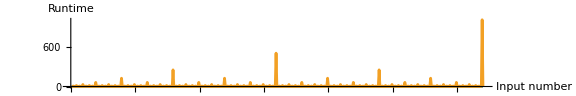

```mathematica
runtimePlot[rtfn[sorted22[[2]],{2,2},9,{8,128}]]
```

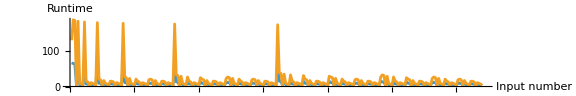

```mathematica
runtimePlot[rtfn[sorted22[[3]],{2,2},8,{8,128}]]
```

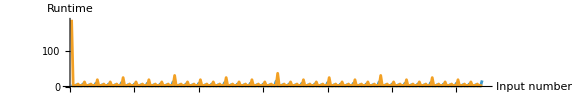

```mathematica
runtimePlot[rtfn[sorted22[[4]],{2,2},8,{8,128}]]
```

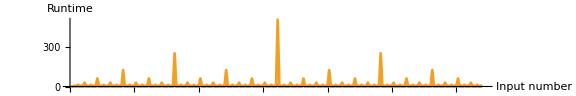

```mathematica
runtimePlot[rtfn[sorted22[[5]],{2,2},8,{8,128}]]
```

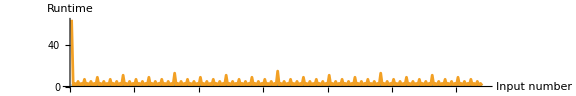

```mathematica
runtimePlot[rtfn[sorted22[[6]],{2,2},8,{8,128}]]
```

```mathematica
rtfn[sorted22[[IntegerPart[Length[sorted22]/2]]],{2,2},9,{16,64}]
```

{{3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,19,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,23,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,19,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,27,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,19,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,23,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,19,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,31,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,19,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,23,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,19,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,27,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,19,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,23,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,19,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,15,1,3,1,7,1,3,1,11,1,3,1,7,1,3,1,35,1}}

```mathematica
runtimePlot[,{3.*Log2[x+1]},x]
```

-Graphics-

example of >=NP

```mathematica
runtimePlot[rtfn[sorted22[[262]],{2,2},9,{8,128}],{446/225*x+129},x]
```

-Graphics-

the drop at the end is because it takes too long so it thinks it doesnt terminate (max is 4*128 = 512)

```mathematica
rtfn[sorted22[[13]],{2,2},9,{8,128}];
```

```mathematica
runtimePlot[,{4.5Log2[x+1]+3},x]
```

-Graphics-

##### max runtime

here we are looking for large runtime small range to look for NP problems

```mathematica
maxrtsorted=SortBy[haltgroups22,-#[[3]]&];
```

```mathematica
rtfn[maxrtsorted[[3]],{2,2},7,{8,128}];
```

this is the same as group 262 from sorting by runtime range NOT THE SAME ANYMORE

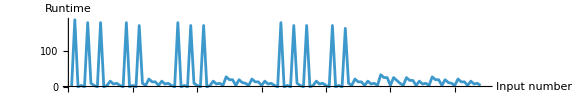

```mathematica
runtimePlot[]
```

```mathematica
rtfn[maxrtsorted[[5]],{2,2},7,{8,128}];
```

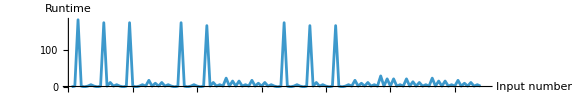

```mathematica
runtimePlot[]
```

```mathematica
rtfn[maxrtsorted[[6]],{2,2},9,{8,128}];
```

```mathematica
runtimePlot[,{1022/485*x},x]
```

example of nicely increasing function

-Graphics-

the drop at the end is because it thinks it doesnt terminate since it takes so long

#### average case

Sorting by average case means we are looking for machines that are capable of having large/small runtimes for many inputs, not necessarily in relation to the inputs (but interestingly enough the distinct top 2 are both clearly increasing)

##### runtime range

```mathematica
sorted22avg=SortBy[haltgroups22avg,-First[#]&];
```

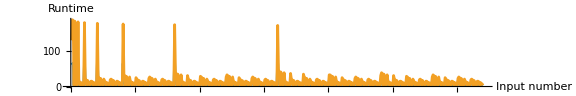

```mathematica
runtimePlot[rtfn[sorted22avg[[1]],{2,2},9,{8,128}]]
```

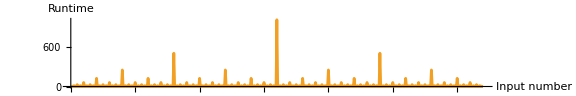

```mathematica
runtimePlot[rtfn[sorted22avg[[2]],{2,2},9,{8,128}]]
```

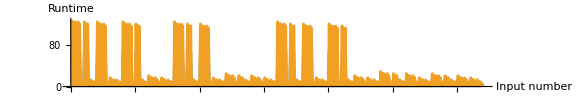

```mathematica
runtimePlot[rtfn[sorted22avg[[3]],{2,2},9,{8,128}]]
```

##### max runtime

```mathematica
maxrtsorted22avg=SortBy[haltgroups22avg,-#[[3]]&];
```

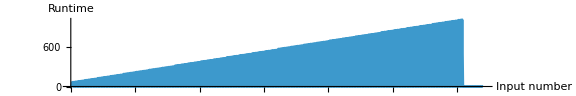

```mathematica
runtimePlot[rtfn[maxrtsorted22avg[[1]],{2,2},9,{8,128}]]
```

```mathematica
rtfn[maxrtsorted22avg[[2]],{2,2},9,{8,128}];
```

```mathematica
runtimePlot[,{6.7*x^0.36+133},x]
```

-Graphics-

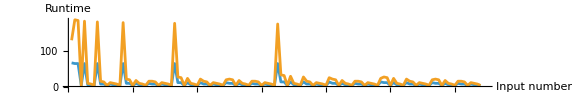

```mathematica
runtimePlot[rtfn[maxrtsorted22avg[[3]],{2,2},7,{8,128}]]
```

```mathematica
runtimePlot[rtfn[maxrtsorted22avg[[4]],{2,2},7,{8,128}]]
```

-Graphics-

If the linear increase is the most we can get for (2,2) machines sorting by max and average runtime, this does not seem promising since linear is not NP. but we can model our input from stephen wolfram nks p. 760 as considering the length of the bits of the input and not the value of the input. This is likely equally valid since turing machine rules are abstract representations of computation that do not align with our current intuition. This may be the case since classical computers are more like RASP’s than turing machines.

#### worse case length (TODO: UPDATE EVERYTHING ELSE UNDERNEATH WITH NEW DATA)

##### runtime range

```mathematica
compress[,Max]
```

{{1,1,1,1,1,1,1,1},{5,13,29,61,125,253,509,1021}}

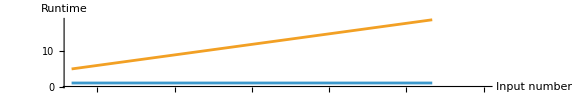
{-Graphics-,-Graphics-}

```mathematica
{runtimePlot[,{4*2^x},x],runtimePlot[compress[,Mean]]}
```

```mathematica
rtfn[sorted22[[4]],{2,2},11,{8,128}];
```

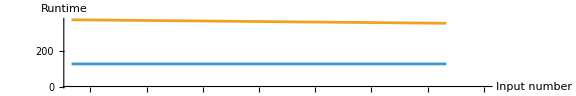
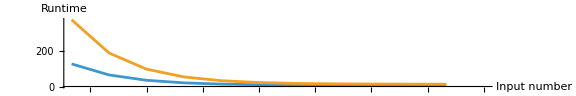

```mathematica
{runtimePlot[compress[,Max]],runtimePlot[compress[,Mean]]}
```

```mathematica
rtfn[sorted22[[262]],{2,2},9,{8,128}];
```

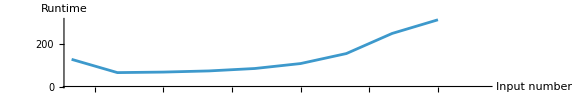
{-Graphics-,-Graphics-}

```mathematica
{runtimePlot[compress[,Max],{1.85*2^x+129},x],runtimePlot[compress[,Mean]]}
```

```mathematica
rtfn[sorted22[[260]],{2,2},12,{8,128}];
```

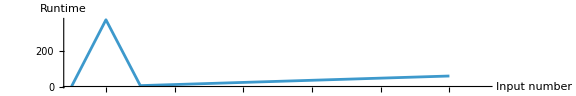

```mathematica
runtimePlot[compress[,Max]]
```

```mathematica
rtfn[sorted22[[261]],{2,2},10,{8,128}];
```

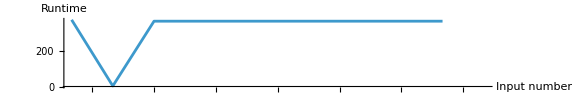
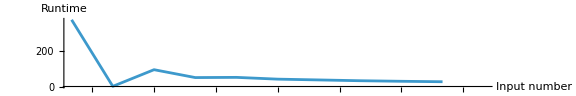

```mathematica
{runtimePlot[compress[,Max]],runtimePlot[compress[,Mean]]}
```

##### max runtime

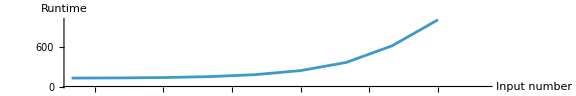

```mathematica
runtimePlot[compress[,Max]]
```

weird shape probably because of the -1 and the drop at the end is because of -1 at the end

```mathematica
runtimePlot[compress[,Mean]]
```

-Graphics-

```mathematica
runtimePlot[compress[,#]]&/@{Max,Mean}
```

{-Graphics-,-Graphics-}

#### worse case with length compressed by average

```mathematica
sorted22lenavg=SortBy[haltgroups22lenavg,-First[#]&];
```

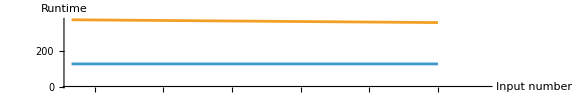
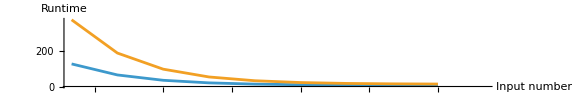

```mathematica
rtfn[sorted22lenavg[[1]],{2,2},9,{8,128}];
runtimePlot[compress[%,#]]&/@{Max,Mean}
```

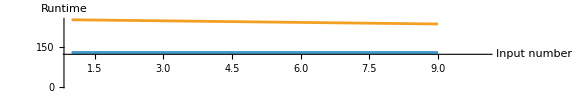
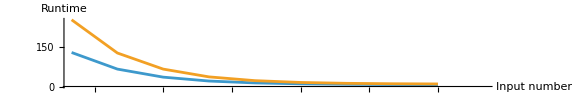

```mathematica
rtfn[sorted22lenavg[[2]],{2,2},9,{8,128}];
runtimePlot[compress[%,#]]&/@{Max,Mean}
```

```mathematica
rtfn[sorted22lenavg[[3]],{2,2},10,{8,128}];
```

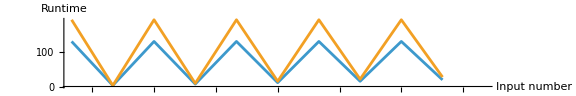
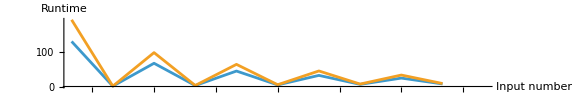

```mathematica
runtimePlot[compress[,#]]&/@{Max,Mean}
```

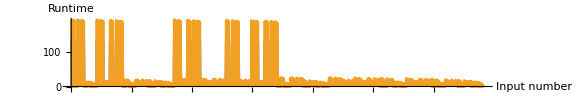

```mathematica
runtimePlot[]
```

#### “increasingness”

```mathematica
sorted22inc=SortBy[haltgroups22leninc,-#[[3]]&];
```

```mathematica
rtfn[sorted22inc[[1]],{2,2},9,{8,128}];
```

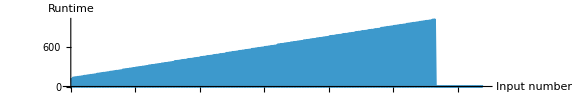
{-Graphics-,-Graphics-}

```mathematica
{runtimePlot[],runtimePlot[compress[,Max]]}
```

```mathematica
rtfn[sorted22inc[[2]],{2,2},10,{8,128}];
```

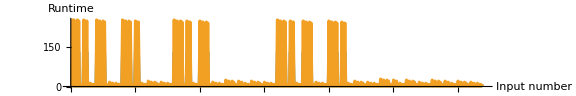
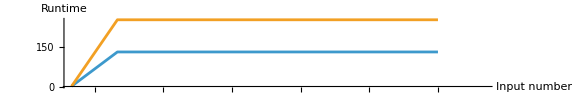

```mathematica
{runtimePlot[],runtimePlot[compress[,Max]]}
```

```mathematica
rtfn[sorted22inc[[3]],{2,2},11,{8,128}];
```

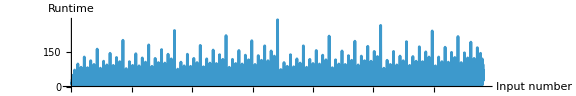
{-Graphics-,-Graphics-}

```mathematica
{runtimePlot[],runtimePlot[compress[,Max],{4.8*x^1.7},x]}
```

```mathematica
rtfn[sorted22inc[[4]],{2,2},11,{8,128}];
```

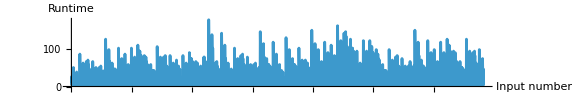
{-Graphics-,-Graphics-}

```mathematica
{runtimePlot[],runtimePlot[compress[,Max],{3*x^1.7+6},x]}
```

### (3,2)

```mathematica
sorted32=SortBy[haltgroups32,-First[#]&];
```

```mathematica
rtfn[sorted32[[1]],{3,2},9,{16,100}]
```

{{3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,11,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,13,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,11,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,15,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,11,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,13,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,11,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,17,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,11,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,13,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,11,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,15,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,11,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,13,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,11,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,9,1,3,1,5,1,3,1,7,1,3,1,5,1,3,1,19},{9,1,25,1,17,1,57,1,9,1,49,1,33,1,121,1,9,1,25,1,17,1,113,1,9,1,97,1,65,1,249,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,241,1,9,1,25,1,17,1,225,1,9,1,193,1,129,1,505,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,121,1,9,1,25,1,17,1,113,1,9,1,97,1,65,1,497,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,481,1,9,1,25,1,17,1,449,1,9,1,385,1,257,1,1017,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,121,1,9,1,25,1,17,1,113,1,9,1,97,1,65,1,249,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,241,1,9,1,25,1,17,1,225,1,9,1,193,1,129,1,1009,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,121,1,9,1,25,1,17,1,113,1,9,1,97,1,65,1,993,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,961,1,9,1,25,1,17,1,897,1,9,1,769,1,513,1,-1,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,121,1,9,1,25,1,17,1,113,1,9,1,97,1,65,1,249,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,241,1,9,1,25,1,17,1,225,1,9,1,193,1,129,1,505,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,121,1,9,1,25,1,17,1,113,1,9,1,97,1,65,1,497,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,481,1,9,1,25,1,17,1,449,1,9,1,385,1,257,1,-1,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,121,1,9,1,25,1,17,1,113,1,9,1,97,1,65,1,249,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,241,1,9,1,25,1,17,1,225,1,9,1,193,1,129,1,-1,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,121,1,9,1,25,1,17,1,113,1,9,1,97,1,65,1,-1,1,9,1,25,1,17,1,57,1,9,1,49,1,33,1,-1,1,9,1,25,1,17,1,-1,1,9,1,1537,1,1025,1,-1}}

```mathematica
runtimePlot[,{8x},x]
```

```mathematica
rtfn[sorted32[[2]],{3,2},9,{4,100}];
```

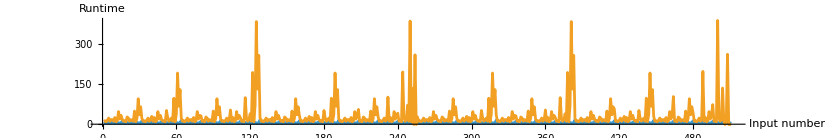

```mathematica
runtimePlot[]
```

```mathematica
Length[#]&/@sorted32
```

```mathematica
rtfn[sorted32[[3]],{3,2},9,{8,100}];
```

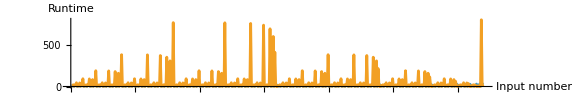

```mathematica
runtimePlot[]
```

```mathematica
rtfn[sorted32[[5]],{3,2},8,{8,100}];
```

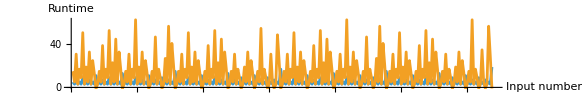

```mathematica
runtimePlot[]
```

```mathematica
rtfn[sorted32[[IntegerPart[Length[sorted32]/2]]],{3,2},9,{8,64}]
```

{{5,1,7,1,9,1,11,1,5,1,7,1,-1,1,11,1,5,1,7,1,13,1,15,1,5,1,7,1,-1,1,15,1,5,1,7,1,9,1,11,1,5,1,7,1,-1,1,11,1,5,1,7,1,-1,1,-1,1,5,1,7,1,19,1,17,1,5,1,7,1,9,1,11,1,5,1,7,1,-1,1,11,1,5,1,7,1,17,1,19,1,5,1,7,1,-1,1,19,1,5,1,7,1,9,1,11,1,5,1,7,1,29,1,11,1,5,1,7,1,-1,1,-1,1,5,1,7,1,23,1,21,1,5,1,7,1,9,1,11,1,5,1,7,1,-1,1,11,1,5,1,7,1,13,1,15,1,5,1,7,1,43,1,15,1,5,1,7,1,9,1,11,1,5,1,7,1,-1,1,11,1,5,1,7,1,-1,1,-1,1,5,1,7,1,19,1,17,1,5,1,7,1,9,1,11,1,5,1,7,1,39,1,11,1,5,1,7,1,-1,1,-1,1,5,1,7,1,-1,1,-1,1,5,1,7,1,9,1,11,1,5,1,7,1,33,1,11,1,5,1,7,1,-1,1,23,1,5,1,7,1,21,1,23,1,5,1,7,1,9,1,11,1,5,1,7,1,-1,1,11,1,5,1,7,1,13,1,15,1,5,1,7,1,-1,1,15,1,5,1,7,1,9,1,11,1,5,1,7,1,55,1,11,1,5,1,7,1,-1,1,-1,1,5,1,7,1,19,1,17,1,5,1,7,1,9,1,11,1,5,1,7,1,-1,1,11,1,5,1,7,1,21,1,23,1,5,1,7,1,-1,1,23,1,5,1,7,1,9,1,11,1,5,1,7,1,29,1,11,1,5,1,7,1,-1,1,-1,1,5,1,7,1,27,1,25,1,5,1,7,1,9,1,11,1,5,1,7,1,51,1,11,1,5,1,7,1,13,1,15,1,5,1,7,1,47,1,15,1,5,1,7,1,9,1,11,1,5,1,7,1,-1,1,11,1,5,1,7,1,33,1,35,1,5,1,7,1,19,1,17,1,5,1,7,1,9,1,11,1,5,1,7,1,43,1,11,1,5,1,7,1,-1,1,-1,1,5,1,7,1,-1,1,-1,1,5,1,7,1,9,1,11,1,5,1,7,1,31,1,11,1,5,1,7,1,-1,1,27,1,5,1,7,1,25,1,27}}

```mathematica
runtimePlot[,{3.5Log2[x+1]},x]
```

-Graphics-

```mathematica
rtfn[sorted32[[IntegerPart[Length[sorted32]/3]]],{3,2},9,{8,64}]
```

{{3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,15,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,15,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,15,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,19,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,15,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,15,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,15,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3,11,3,3,3,7,3,3,3,7,3,3,3,7,3,3,3}}

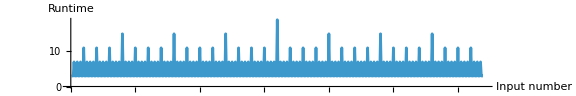

```mathematica
runtimePlot[]
```

```mathematica
rtfn[sorted32[[IntegerPart[Length[sorted32]/4]]],{3,2},8,{4,64}]
```

{{1,-1,1,9,1,9,1,-1,1,-1,1,11,1,11,1,15,1,15,1,9,1,9,1,15,1,15,1,13,1,13,1,-1,1,-1,1,9,1,9,1,-1,1,-1,1,11,1,11,1,17,1,17,1,9,1,9,1,17,1,17,1,15,1,15,1,21,1,21,1,9,1,9,1,21,1,21,1,11,1,11,1,15,1,15,1,9,1,9,1,15,1,15,1,13,1,13,1,21,1,21,1,9,1,9,1,21,1,21,1,11,1,11,1,19,1,19,1,9,1,9,1,19,1,19,1,17,1,17,1,-1,1,-1,1,9,1,9,1,-1,1,-1,1,11,1,11,1,15,1,15,1,9,1,9,1,15,1,15,1,13,1,13,1,-1,1,-1,1,9,1,9,1,-1,1,-1,1,11,1,11,1,17,1,17,1,9,1,9,1,17,1,17,1,15,1,15,1,23,1,23,1,9,1,9,1,23,1,23,1,11,1,11,1,15,1,15,1,9,1,9,1,15,1,15,1,13,1,13,1,23,1,23,1,9,1,9,1,23,1,23,1,11,1,11,1,21,1,21,1,9,1,9,1,21,1,21,1,19,1,19,1},{1,-1,1,11,1,11,1,-1,1,-1,1,13,1,13,1,19,1,19,1,11,1,11,1,19,1,19,1,15,1,15,1,-1,1,-1,1,11,1,11,1,-1,1,-1,1,13,1,13,1,21,1,21,1,11,1,11,1,21,1,21,1,17,1,17,1,27,1,27,1,11,1,11,1,27,1,27,1,13,1,13,1,19,1,19,1,11,1,11,1,19,1,19,1,15,1,15,1,27,1,27,1,11,1,11,1,27,1,27,1,13,1,13,1,23,1,23,1,11,1,11,1,23,1,23,1,19,1,19,1,-1,1,-1,1,11,1,11,1,-1,1,-1,1,13,1,13,1,19,1,19,1,11,1,11,1,19,1,19,1,15,1,15,1,-1,1,-1,1,11,1,11,1,-1,1,-1,1,13,1,13,1,21,1,21,1,11,1,11,1,21,1,21,1,17,1,17,1,29,1,29,1,11,1,11,1,29,1,29,1,13,1,13,1,19,1,19,1,11,1,11,1,19,1,19,1,15,1,15,1,29,1,29,1,11,1,11,1,29,1,29,1,13,1,13,1,25,1,25,1,11,1,11,1,25,1,25,1,21,1,21,1}}

```mathematica
runtimePlot[,{3.5Log2[x+1]+1},x]
```

-Graphics-

Everything with a small range seems to also have low asymptotic runtimes (e.g. a lot of small constants and logs)?? where is the large runtime small range?

```mathematica
sorted23=SortBy[haltgroups23,-First@#&];
```

Out of the first 20 equivalence classes for (2,2) machines, 10 groups generally had logarithmic behavior, and some groups seem to oscillate from 0 to a constant maximum. It is difficult to extrapolate the ultimate behavior of these oscillating plots, but I suspect they are most likely constant and possibly logarithmic. One of these graphs is group 2 (see below), which seems to model a triangle wave and thus be considered constant. However, group 10 may imply that the graphs like group 2 (potentially excluding itself) may be part of a larger graph that only becomes emergent for large inputs.

```mathematica
Block[{states=2,symbols=2},
With[
{
dx=2.5,
bits=8,
data=DeleteDuplicates[
ParallelMap[
htDP[#,8,8,64]&,
sorted22[[10,5;;]]
][[All,1]]
]
},
Show[
Plot[
5.3*Log2[x+1]+2.5,
{x,0,2^bits-1},
PlotStyle->{Dashed,Thickness[0.0025]},
PlotRange->All,
PlotLabels->"Expressions"
],
ListPlot[
data,
DataRange->{0,Length@data[[1]]-1},
Joined->True,
PlotRange->All
],
AxesOrigin->{0,0},
AspectRatio->1/6,
ImageSize->{1000,Automatic},
AxesLabel->{"Input number", "Runtime"},
PlotLabel->"(2,2) group 10 runtime",
PerformanceGoal->"Speed"
]
]
]//Rasterize
```

-Graphics-

There are also cases where the runtime is linear, such as (2,2) group 262.

```mathematica
Block[{states=2,symbols=2},
With[
{
bits=8,
data=DeleteDuplicates[
ParallelMap[
htDP[#,8,8,64]&,
sorted22[[262,5;;]]
][[All,1]]
]
},
Show[
Plot[
2*x+130,
{x,0,2^bits-1},
PlotStyle->{Dashed,Thickness[0.0025]},
PlotRange->All,
PlotLabels->"Expressions"
],
ListPlot[
data,
DataRange->{0,Length@data[[1]]-1},
Joined->True,
PlotRange->All
],
AxesOrigin->{0,0},
AspectRatio->1/6,
ImageSize->{1000,Automatic},
AxesLabel->{"Input number", "Runtime"},
PlotLabel->"(2,2) group 262 runtime",
PerformanceGoal->"Speed"
]
]
]//Rasterize
```

-Graphics-

For (2,3) machines, the overall behavior is harder to see generally because the number of rules in a group can be very large so we must process subsets of data at a time. We can also refer to the (2,3) graph at the beginning of the section and find groups that have small group size, such as 3, 8, 12, and 13. Generally, this subset of groups seems to show that (2,3) runtimes are more chaotic than (2,2). A notable group in (2,3) is group 12, where there is one Turing machine that seems to represent a total function that runs in constant time while all others run in approximately logarithmic time.

```mathematica
Block[{states=2,symbols=3},
With[
{
bits=8,
data=DeleteDuplicates[
ParallelMap[
htDP[#,8,8,64]&,
sorted23[[12,5;;]]
][[All,1]]
]
},
Show[
Plot[
6*Log2[x+1],
{x,0,2^bits-1},
PlotStyle->{Dashed,Thickness[0.0025]},
PlotRange->All,
PlotLabels->"Expressions"
],
ListPlot[
data,
DataRange->{0,Length@data[[1]]-1},
Joined->True,
PlotRange->All
],
AspectRatio->1/6,
ImageSize->{1000,Automatic},
AxesOrigin->{0,0},
AxesLabel->{"Input number", "Runtime"},
PlotLabel->"(2,2) group 10 runtime",
PerformanceGoal->"Speed"
]
]
]//Rasterize
```

-Graphics-

## Conclusions

To address the title of this essay, the similarity between the shapes of the minimum and maximum runtime graphs indicates that functions with a bad worse-case running time will also have a relatively worse best-case running time, and fast minimum runtimes will also have faster maximum runtimes. If we view these functions as algorithms, we hypothesize that problems solved with slower unoptimized algorithms will also likely be solved with slower optimal algorithms if we look at the space of all problems. Of course this is not always true: sorting algorithms are one example where there exists a vast pool of algorithms with a large range of runtimes. However, that the runtime range in all our plots decrease very quickly in the set of all rule groups (similar to ), where the left represents the rare case where runtime can be significantly improved (e.g. sorting). Sorting the data by maximum runtime, we can also observe that there are occasional drops in minimum runtime, yet most of the time they are identical. I believe that the small section of large runtime range represents a subset of P problems which can be solved both quickly and very slowly. The gradual convergence of minimum and maximum runtime could be analogous to the runtime of the best possible algorithm approaching brute-force. 

THIS DOESNT REALLY MAKE SENSE SINCE THE CARDINALITY OF ALL COMPLEXITY CLASSES IS aleph null WHICH IS COUNTABLY INFINITE
This conclusion is not without flaw, however, since P and NP are not the only complexity classes. Without specific comparisons between the complexity classes, my interpretation would be equally valid if we took P to equal NP and claim that the cardinality of NP (which contains P and its subsets) is significantly smaller than the cardinality of the difference between EXPTIME and NP, or that the time difference between P and NP is similar to the difference between NP and EXPTIME.

Looking specifically at individual runtime plots, I did not find a large difference between the asymptotic behavior of each rule for most groups. Most groups with large runtime ranges mostly consist of asymptotically logarithmic and constant worse-case runtime. This is further evidence that empirical tests should be weighted equally to theory, since in one case, a large runtime range occurs because of a Turing machine that runs in “constant time” asymptotically, but this constant is very large. One such example is (2,3) group 45.

## Future Directions

As mentioned, I first want to look into the plot of rule number distributions and precisely identify and analyze patterns in that plot. More generally, I could generate, visualize, and analyze data for all computable  pairs (when ). Before this can happen, I would need to further optimize my implementation to make larger computations feasible. The goal of generality for this project was not fully achieved due to all the constraints, so future work generalizes this further by having arbitrary halt states and carefully chosen constraints instead of the arbitrary ones we set in this project. The ultimate goal in the future would to find interesting cases of runtimes within each equivalence class and to better quantify the relationship between the runtime of a Turing machine and a conventional computer to draw more precise conclusions. Depending on the results, this project could also be extended to graph Turing machines.

## Acknowledgements

I would like to thank my mentor Felipe Amorim for supporting me throughout this project, keeping me on track, and helping me organize and implement my ideas. I would also like to thank my teaching assistant Gregory Roudenko for inspiring the methods I used for code optimization, mentor Shenghui Yang for explaining code compilation and approaches to code optimization, and the program directors Rory Foulger, Megan Davis, and Eryn Gillam for accepting me into WSRP. Finally, I would like to thank Dr. Stephen Wolfram for giving me this illuminating project and its motivation as an unconventional approach to complexity theory.

## References

6.045 Lecture 13: Time complexity. (n.d.). https://people.csail.mit.edu/rrw/6.045-2020/lec13-color.pdf

Ariel (https://cs.stackexchange.com/users/27055/ariel), Given two total Turing machines, is it undecidable problem to detect whether they give the same output on all inputs?, URL (version: 2015-08-30): https://cs.stackexchange.com/q/45687

Manlio (https://math.stackexchange.com/users/22701/manlio), How are weakly universal Turing machines actually defined?, URL (version: 2020-04-22): https://math.stackexchange.com/q/3634837

Weisstein, Eric W. “Turing Machine.” From MathWorld--A Wolfram Resource. https://mathworld.wolfram.com/TuringMachine.html

Wikipedia contributors. (2025, June 30). Automata theory. In Wikipedia, The Free Encyclopedia. Retrieved 15:56, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Automata_theory&oldid=1298074772

Wikipedia contributors. (2025, April 14). DFA minimization. In Wikipedia, The Free Encyclopedia. Retrieved 15:59, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=DFA_minimization&oldid=1285525404

Wikipedia contributors. (2025, June 12). Halting problem. In Wikipedia, The Free Encyclopedia. Retrieved 21:23, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Halting_problem&oldid=1295203495

Wikipedia contributors. (2025, March 18). Rice’s theorem. In Wikipedia, The Free Encyclopedia. Retrieved 15:58, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Rice%27s_theorem&oldid=1281112418

Wikipedia contributors. (2025, June 24). Turing machine. In Wikipedia, The Free Encyclopedia. Retrieved July 2, 2025, from https://en.wikipedia.org/w/index.php?title=Turing_machine&oldid=1297184647

Wikipedia contributors. (2025, March 17). Universal Turing machine. In Wikipedia, The Free Encyclopedia. Retrieved 15:55, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Universal_Turing_machine&oldid=1281033475

Wolfram, S. (2002). A New Kind of Science. Retrieved from https://www.wolframscience.com

$Aborted